```mathematica
Quit[]
```

# Calculations

```mathematica
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
(*Ниже идет расчет гамма тау*)
```

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ScalarProduct[p1,p1]=m1^2;
ScalarProduct[p2,p2]=m2^2;
ScalarProduct[p1,p2]=(m1^2+m2^2-q2)/2;
q=p1-p2;
H =SpinorUBar[p2,m2].GA[μ].(1+GA[5]).SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
H2=H*cH;
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[q,μ]*FV[q,α]-q2*MT[μ,α])]];

HT:=λ*H4;
```

Calculations

## Initial constants

```mathematica
Y=1/2;
Gf=1.166*10^(-5);
dm232=1;
a1=1.07;
Fm2320=1/(3*π);
mπ=0.13957061;
fπ=0.1304;
mρ=0.7665;
fρ=0.216;
ma1=1.230;
fa1=0.238;
SetAttributes[V,Orderless];
V["c","b"]=0.0411;V["c","s"]=0.974;V["c","d"]=0.225;
V["u","b"]=0.00357;V["u","s"]=0.225;V["u","d"]=0.974;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Fq2π=ReadList["plot2pi.txt",{Number,Number}];
Fq3π=ReadList["plot3pi.txt",{Number,Number}];
Fq4π=ReadList["plot4pi.txt",{Number,Number}];
Fq5π=ReadList["plot5pi.txt",{Number,Number}];
```

```mathematica
test=1;
Interpolation[Fq2π][test]
```

0.0341817

## Initial Tau lepton calculations for constants 3pi 5pi

```mathematica
(*τ->3π*)
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ScalarProduct[p1,p1]=m1^2;
ScalarProduct[p2,p2]=m2^2;
ScalarProduct[p1,p2]=(m1^2+m2^2-q2)/2;
q=p1-p2;
H =SpinorUBar[p2,m2].GA[μ].(1+GA[5]).SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
H2=H*cH;
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[q,μ]*FV[q,α]-q2*MT[μ,α])]];
λ:=√(1-((m2+√q2)/m1)^2)*√(1-((m2-√q2)/m1)^2);
HT:=λ*H4;
HT;
dΓ3π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq3π][q2];
(*Decay to 3π*)
m1=1.776;
m2=0;
h=6.5*10^-25;τ=290*10^-15;
Γτ=h/τ;
Const3π=1;
Γ3π=NIntegrate[dΓ3π, {q2,9mπ^2,(m1-m2)^2}];
Clear[Const3π];
Br=Γ3π/Γτ;
BrNorm=0.0903;
Clear[Const3π];
Const3π =BrNorm/Br
Γ3π=Const3π*NIntegrate[dΓ3π, {q2,9mπ^2,(m1-m2)^2}];
Br=Γ3π/Γτ;
Error=Br/BrNorm
```

7.01631

1.

```mathematica
(*Считаем константу для распада тау лептона в пять пи мезонов*)
Clear[Br,BrNorm];
dΓ5π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq5π][q2];
Γ5π=NIntegrate[dΓ5π, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5π/Γτ;
BrNorm=0.000769;
Const5π=BrNorm/Br
Γ5π=Const5π*NIntegrate[dΓ5π, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5π/Γτ;
Error=Br/BrNorm
```

32955.6

1.

```mathematica
Clear[Br,BrNorm];
dΓ2π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq2π][q2];
Γ2π=NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
BrNorm=0.2549;
Const2π=BrNorm/Br
Γ2π=Const2π*NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
Error=Br/BrNorm
```

0.352572

1.

```mathematica
Clear[Br,BrNorm];
Fq2πb=(0.0013516183448589506*(1+0.6384423540947195*q2)*(-0.07840000000000001+q2)^2)/((0.013064170424296547+(-0.5686550420645691+q2)^2)*q2^2);
dΓ2πb= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq2πb;
Γ2πb=NIntegrate[dΓ2πb, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2πb/Γτ;
BrNorm=0.2549;
Const2πbefore=BrNorm/Br
Γ2πb=Const2πbefore*NIntegrate[dΓ2πb, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2πb/Γτ;
Error=Br/BrNorm
```

1.25599

1.

```mathematica
Clear[Br,BrNorm];
dΓ4π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq4π][q2];
Γ4π=NIntegrate[dΓ4π, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4π/Γτ;
BrNorm=0.0462;
Const4π=BrNorm/Br
Γ4π=Const4π*NIntegrate[dΓ4π, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4π/Γτ;
Error=Br/BrNorm
```

10884.

1.

## Clear

```mathematica
Clear[Γ2π,Γ3π,Γ4π,Γ5π,dΓ2π,dΓ3π,dΓ4π,dΓ5π,H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ClearScalarProducts;
```

## Init

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,m232,q,m1,m2,m3,m4,Br,f1,f2,g1,g2];
ScalarProduct[p11,p11]=m1^2;
ScalarProduct[p22,p22]=m2^2;
ScalarProduct[p11,p22]=(m1^2+m2^2-m232)/2;
SetMandelstam[m232,m132,m122,p1,-p2,-pe,-ke,m1,m2,0,0];
qq=p11-p22;
q=p1-p2;
sigma=I*(GA[μ].GA[ν]-GA[ν].GA[μ])/2;
H =SpinorUBar[p22,m2].(GA[μ]*f1+I*sigma*FV[qq,ν]*f2/m1).SpinorU[p11, m1]-SpinorUBar[p22,m2].(GA[μ]*g1+ⅈ*sigma*FV[qq,ν]*g2/m1).GA[5].SpinorU[p11, m1];
HH=SpinorUBar[p2,m2].(GA[μ]*f1+I*sigma*FV[q,ν]*f2/m1).SpinorU[p1, m1]-SpinorUBar[p2,m2].(GA[μ]*g1+ⅈ*sigma*FV[q,ν]*g2/m1).GA[5].SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
cHH= ComplexConjugate[HH]/.{μ->α,ν->β};
H2=H*cH;
HH2=HH*cHH;
HH3=DiracSimplify[FermionSpinSum[HH2]]/.{DiracTrace->TR};
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α]-m232*MT[μ,α])]];
λ:=√(1-((m2+√m232)/m1)^2)*√(1-((m2-√m232)/m1)^2);
HT:=λ*H4;
(*T=Transversal*)
HL:=λ*Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α])]];
(*L=Longitudinal*)
L=SpinorUBar[pe].GA[μ].(1+GA[5]).SpinorV[ke];
cL=ComplexConjugate[L]/.{μ->α};
L2=FermionSpinSum[L*cL]/.{DiracTrace->TR};
M2=Simplify[1/2*Gf^2*Calc[HH3*L2]];
M3=M2//.m132->m1^2+m2^2-m122-m232;
E2ZV= (m122-m2^2 +m3^2)/(2*Sqrt[m122]) (*  E2^*  *);
E3ZV= (m1^2-m122-m4^2)/(2*Sqrt[m122])  (*  E3^*  *);
m23min=(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]+Sqrt[E3ZV^2-m4^2])^2;
m23max=Simplify[Calc[(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]-Sqrt[E3ZV^2-m4^2])^2]];
m12min=m2^2;
m12max=m1^2;
```

```mathematica
dΓl:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*dm232 /(2*π)*(1/(8*π))*Vckm^2*HT*Fm2320
dΓl1:=(1/2)*(1/(2*π)^3)*(1/(32*m1^3))*Vckm^2*M3;

Fq2πbefore:=Const2πbefore*(0.0013516183448589506*(1+0.6384423540947195*m232)*(-0.07840000000000001+m232)^2)/((0.013064170424296547+(-0.5686550420645691+m232)^2)*m232^2);
Fq3πbefore:=Const3π*2.93*10^-5*((m232-9*mπ^2)/m232)^4*(1+190m232)/(((m232-1.06)^2+0.48)^2);
Fq4πbefore:=Const4π* (0.00017983715820604627*(-0.31360000000000005+m232)*(1+5.074780646730226*m232+8.631754238222705*m232^2))/((0.6162735882355033+(-1.834698151162789+m232)^2)^2*m232);
Fq5πbefore:=Const5π*32*((m232-25*mπ^2)/m232)^10*(1-1.65*m232+0.69m232^2)/(((m232+2.21)^2-4.69)^3);


ret1=BWr[q]*ComplexConjugate[BWr[q]];
mpi=0.13957018;
ret2=ret1*(4*mpi^2-q*q);
ret3=ret2/(-3 q*q);
λr=Sqrt[(q^2-4 mpi^2)/q^2];
ret4=ret3*λr/(8 π);
ret5=ret4/.{q->Sqrt[m232]};
Fq2πn=Const2π*Fq2π;
Fq3πn=Const3π*Fq3π;
Fq4πn=Const4π*Fq4π;
Fq5πn=Const5π*Fq5π;
dΓ2π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Interpolation[Fq2πn][m232];
dΓ3π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Interpolation[Fq3πn][m232];
dΓ4π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Interpolation[Fq4πn][m232];
dΓ5π:=  (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Interpolation[Fq5πn][m232];
dΓ2πbefore:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq2πbefore;
dΓ3πbefore:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq3πbefore;
dΓ4πbefore:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq4πbefore;
dΓ5πbefore:=  (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq5πbefore;
```

## File

```mathematica
SetDirectory[NotebookDirectory[]];
<<"wang_data.m";
decays={#["in"],#["out"]}&/@Normal[DeleteDuplicates[dsFF[All,{"in","out"}]]];
Clear[$FF];
$FF[data_]:=Module[{},Switch[data["func"],"FF",Return[data["F0"]/(1-m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];,"GG",Return[data["F0"]/(1+m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];];];
(*Clear[cS,cA];*)
Clear[FF];
FF[query_]:=Module[{$res},$res=dsFF[query];
Return[cS $FF[$res[1]]+cA $FF[$res[2]]]];
```

## Test

```mathematica
in="\\Omega_{cc}^{+}";
out="\\Omega_{c}^{0}";
testresult={};
AppendTo[testresult,{"in","out","l nul" ,"pi","rho","3 pi","a1","5 pi"}];
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*a1*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*a1*Vckm^2*Hπ;
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γa1=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\a_1"]&]][[1]]["width"];
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
AppendTo[testresult,{in,out,Floor[Chop[Γl1/fullΓ],-0.00001]*100,Floor[Chop[Γπ/fullΓ],-0.00001]*100,Floor[Chop[Γρ/fullΓ],-0.00001]*100, Floor[Chop[Γ3π/fullΓ],-0.00001]*100,Floor[Chop[Γa1/fullΓ],-0.00001]*100,Floor[Chop[Γ5π/fullΓ],-0.000001]*100}];
testresult
```

(in | out | l nul | pi | rho | 3 pi | a1 | 5 pi
\Omega_{cc}^{+} | \Omega_{c}^{0} | 6.661 | 6.951 | 24.136 | 0. | 100 Floor[4.10494×10^11 Missing[PartAbsent,1][width],-0.00001] | 0.)

```mathematica
Γa1=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"a_{1}"]&]][[1]]["width"]
```

Missing[PartAbsent,1][width]

## Main calculation

```mathematica
result={};
AppendTo[result,{"in","out","Vckm","l nul","pi" ,"rho/2pi","2 pi after / 2 pi before","3 pi","4 pi","5 pi"}];
i=.0;
PrintTemporary[Dynamic[dec],"Завершено",Dynamic[Floor[i/36*100,-0.1]], "%" ];
Do[
{in,out}=dec;
i=i+1;
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*Vckm^2*Hπ;
Ha1=HT/.{m232-> ma1^2};
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γ2π=NIntegrate[dΓ2π, {m232,4mπ^2,(m1-m2)^2}];
Γ2πbefore=NIntegrate[dΓ2πbefore, {m232,4mπ^2,(m1-m2)^2}];
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ4π=NIntegrate[dΓ4π, {m232,16mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
AppendTo[result,{in,out,Vckm1->Vckm2,Floor[Chop[Γl1/fullΓ],-0.000001]*100,Floor[Chop[Γπ/fullΓ],-0.0000000001]*100,Floor[Chop[Γρ/Γ2π],-0.00000001],Floor[Chop[Γ2π/Γ2πbefore],-0.0000001],Floor[Chop[Γ3π/fullΓ],-0.0000001]*100,Floor[Chop[Γ4π/fullΓ],-0.0000001]*100,Floor[Chop[Γ5π/fullΓ],-0.0000001]*100}];
,{dec,decays}];
result
```

$Aborted

(in | out | Vckm | l nul | pi | rho/2pi | 2 pi after / 2 pi before | 3 pi | 4 pi | 5 pi
\Xi_{cc}^{++} | \Lambda_{c}^{+} | c→d | 0.4936 | 0.220173 | 2.93949 | 0.3908 | 0. | -0.0004 | 0.
\Xi_{cc}^{++} | \Sigma_{c}^{+} | c→d | 0.4503 | 0.175318 | 3.721 | 0.311575 | 0. | -0.00038 | 0.)

```mathematica
in="\\Xi_{bc}^{0}";
out="\\Sigma_{c}^{+}";
testresult={};
AppendTo[testresult,{"in","out","l nul" ,"pi","rho","3 pi","a1","5 pi"}];
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*a1*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*a1*Vckm^2*Hπ;
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γa1=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\a_1"]&]][[1]]["width"];
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
AppendTo[testresult,{in,out,Floor[Chop[Γl1/fullΓ],-0.00001]*100,Floor[Chop[Γπ/fullΓ],-0.00001]*100,Floor[Chop[Γρ/fullΓ],-0.00001]*100, Floor[Chop[Γ3π/fullΓ],-0.00001]*100,Floor[Chop[Γa1/fullΓ],-0.00001]*100,Floor[Chop[Γ5π/fullΓ],-0.000001]*100}];
testresult
```

(in | out | l nul | pi | rho | 3 pi | a1 | 5 pi
\Xi_{bc}^{0} | \Sigma_{c}^{+} | 0.001 | 0.001 | 0.001 | 0.001 | 100 Floor[1.41432×10^11 Missing[PartAbsent,1][width],-0.00001] | 0.0001)

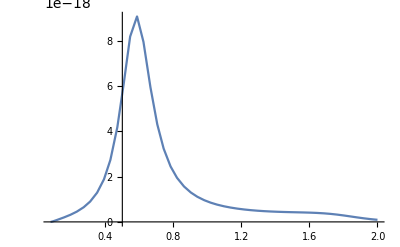

```mathematica
Plot[dΓ2π,{m232, 4 mpi^2, 2}, PlotRange-> All]
```

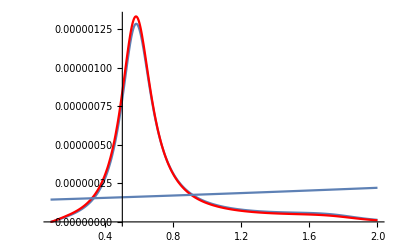

```mathematica
Show[Plot[dΓ2π/fullΓ,{m232, 4 mpi^2, 2}, PlotRange-> All],Plot[Fq2π/100000,{m232, 4 mpi^2, 2}, PlotRange-> All, PlotStyle->Red], Plot[dΓl/fullΓ,{m232,  4 mpi^2, 2}, PlotRange-> All],PlotRange-> All]
```

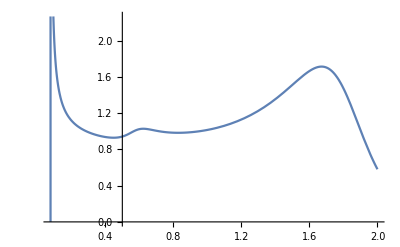

```mathematica
Plot[Fq2π/Fq2πbefore, {m232, 4mpi^2, 2}]
```

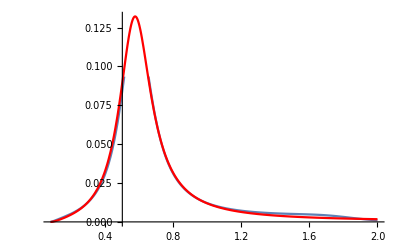

```mathematica
Show[Plot[Fq2π,{m232, 4mpi^2, 2}],Plot[Fq2πbefore,{m232, 4mpi^2, 2},PlotStyle-> Red], PlotRange-> All]
```